```mathematica
(*Factors={1,2,3,12,13,23,123}*)
Factors=Times@@@Subsets[Transpose@Tuples[{1,-1},3],{1,3}];
(*Rearrange*)
(*Rearrange the numbers in the RHS to obtain different combinations*)
Factors[[{1,2,3,4,5,6,7}]]=Factors[[{1,2,3,4,5,6,7}]];
Factors=Transpose[Factors];
```

```mathematica
prob[n_,q_]:=Module[{i,j,k,l},

(*q=100/100*)
s=1-q;
r=2*q-1;


(*Change states here*)



meas=Map[Normalize,{{1,0,0},{0,1,0}}];

meas=Map[Normalize,{{0,0,1},{1,0,0},{-1,0,0},{-1,0,0},{-1,0,0}}];
meas=Map[Normalize,{{1,0,0},{-1,0,0},{0,0,1},{0,1,0},{1,0,0},{1,0,0}}];

meas=Map[Normalize,{{1,0,0},{0,1,0},{0,0,1}}];



encod=Map[Normalize,Map[Table[Subscript[v, j],{j,1,n}].#&,Factors[[1;;8,1;;n]]]/.Subscript[v, k_]->meas[[k]]];
encod=Table[{encod[[l,1]],encod[[l,2]]*r,encod[[l,3]]*r},{l,1,8}];
(*t=Table[1/Sqrt[1-4*s*q*(Nor[[j,2]]^2+Nor[[j,3]]^2)],{j,1,8}];
encod=Table[{t[[c]]*Nor[[c,1]],t[[c]]*Nor[[c,2]]*r^2,t[[c]]*Nor[[c,3]]*r^2},{c,1,8}];
Print["meas=",meas];Print["encod=",encod];*)
f[i_,j_]:=Dot[meas[[i]],encod[[j]]]*Factors[[j,i]];
p=N[(1+Total[Flatten [Array[f,{n,8}]]]/(n*8))/2]
(*Print["p=",p];
Print["Blue -> Encoded Strings, Red-> Up of Measurement"];
ac=Table[Graphics3D[{Arrow[{{0,0,0},meas[[i]]}]}],{i,1,Length[meas]}];
Show[SphericalPlot3D[1,{phi,0,2Pi},{theta,0,Pi},Mesh->None,PlotStyle->Directive[White,Opacity[0.2]]],ListPointPlot3D[encod,PlotStyle->Directive[Blue,PointSize->.03]],ListPointPlot3D[meas,PlotStyle->Directive[Red,PointSize-> 0.02]],Graphics3D[{Red,Arrow[{{0,0,0},{1,0,0}}]}],Graphics3D[{Red,Arrow[{{0,0,0},{0,1,0}}]}],Graphics3D[{Red,Arrow[{{0,0,0},{0,0,1}}]}],ConvexHullMesh[encod,MeshCellStyle->{{2,All}->Opacity[0.2,Yellow]}],ac]*)]
```

```mathematica
prob[3,1]
```

Part::pkspec1: The expression k cannot be used as a part specification.

0.788675

```mathematica
three=Array[prob,{1,50},{3,{51/100,100/100}}]
```

Part::pkspec1: The expression k cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{0.600074,0.603923,0.607772,0.611621,0.61547,0.619319,0.623168,0.627017,0.630866,0.634715,0.638564,0.642413,0.646262,0.650111,0.65396,0.657809,0.661658,0.665507,0.669356,0.673205,0.677054,0.680903,0.684752,0.688601,0.69245,0.696299,0.700148,0.703997,0.707846,0.711695,0.715544,0.719393,0.723242,0.727091,0.73094,0.734789,0.738638,0.742487,0.746336,0.750185,0.754034,0.757883,0.761732,0.765581,0.76943,0.773279,0.777128,0.780977,0.784826,0.788675}}

```mathematica
three={{0.6000740466595351,0.6039230484541326,0.6077720502487302,0.6116210520433276,0.6154700538379252,0.6193190556325227,0.6231680574271202,0.6270170592217177,0.6308660610163151,0.6347150628109127,0.6385640646055102,0.6424130664001078,0.6462620681947052,0.6501110699893027,0.6539600717839003,0.6578090735784977,0.6616580753730953,0.6655070771676928,0.6693560789622902,0.6732050807568877,0.6770540825514852,0.6809030843460828,0.6847520861406803,0.6886010879352777,0.6924500897298753,0.6962990915244728,0.7001480933190702,0.7039970951136678,0.7078460969082653,0.7116950987028627,0.7155441004974603,0.7193931022920579,0.7232421040866552,0.7270911058812528,0.7309401076758504,0.7347891094704477,0.7386381112650453,0.7424871130596429,0.7463361148542403,0.7501851166488378,0.7540341184434354,0.7578831202380328,0.7617321220326303,0.7655811238272279,0.7694301256218253,0.7732791274164229,0.7771281292110204,0.7809771310056178,0.7848261328002154,0.7886751345948129}};
```

```mathematica
six={{0.6374435911228339,0.6388044187577134,0.640165246392593,0.6415260740274725,0.6428869016623521,0.6442477292972316,0.6456085569321112,0.6469693845669906,0.6483302122018701,0.6496910398367498,0.6510518674716294,0.6524126951065088,0.6537735227413884,0.655134350376268,0.6564951780111474,0.657856005646027,0.6592168332809065,0.6605776609157861,0.6619384885506657,0.6632993161855452,0.6646601438204247,0.6660209714553043,0.6673817990901838,0.6687426267250633,0.6701034543599429,0.6714642819948224,0.672825109629702,0.6741859372645815,0.6755467648994611,0.6769075925343406,0.6782684201692202,0.6796292478040997,0.6809900754389793,0.6823509030738588,0.6837117307087384,0.6850725583436179,0.6864333859784975,0.687794213613377,0.6891550412482566,0.6905158688831361,0.6918766965180156,0.6932375241528952,0.6945983517877747,0.6959591794226543,0.6973200070575338,0.6986808346924134,0.7000416623272929,0.7014024899621724,0.702763317597052,0.7041241452319316}};
```

```mathematica
five={{0.6797798653909831,0.680674292581983,0.681568719772983,0.6824631469639828,0.6833575741549828,0.6842520013459826,0.6851464285369826,0.6860408557279825,0.6869352829189824,0.6878297101099823,0.6887241373009823,0.6896185644919821,0.6905129916829821,0.691407418873982,0.6923018460649819,0.6931962732559818,0.6940907004469817,0.6949851276379817,0.6958795548289816,0.6967739820199815,0.6976684092109814,0.6985628364019814,0.6994572635929812,0.7003516907839812,0.701246117974981,0.702140545165981,0.7030349723569809,0.7039293995479808,0.7048238267389808,0.7057182539299807,0.7066126811209805,0.7075071083119805,0.7084015355029805,0.7092959626939803,0.7101903898849802,0.7110848170759801,0.7119792442669801,0.71287367145798,0.7137680986489798,0.7146625258399798,0.7155569530309798,0.7164513802219796,0.7173458074129795,0.7182402346039795,0.7191346617949794,0.7200290889859793,0.7209235161769793,0.7218179433679791,0.7227123705589791,0.7236067977499789}};
```

```mathematica
two={{0.6803122292025696,0.6838477631085024,0.6873832970144351,0.6909188309203678,0.6944543648263006,0.6979898987322333,0.701525432638166,0.7050609665440988,0.7085965004500315,0.7121320343559643,0.7156675682618969,0.7192031021678297,0.7227386360737624,0.7262741699796953,0.7298097038856279,0.7333452377915607,0.7368807716974934,0.7404163056034262,0.7439518395093588,0.7474873734152916,0.7510229073212243,0.7545584412271571,0.7580939751330897,0.7616295090390226,0.7651650429449552,0.7687005768508881,0.7722361107568207,0.7757716446627535,0.7793071785686863,0.7828427124746191,0.7863782463805518,0.7899137802864844,0.7934493141924173,0.7969848480983499,0.8005203820042827,0.8040559159102154,0.8075914498161482,0.8111269837220809,0.8146625176280136,0.8181980515339464,0.8217335854398791,0.8252691193458118,0.8288046532517446,0.8323401871576772,0.8358757210636101,0.8394112549695428,0.8429467888754756,0.8464823227814082,0.850017856687341,0.8535533905932737}};
```

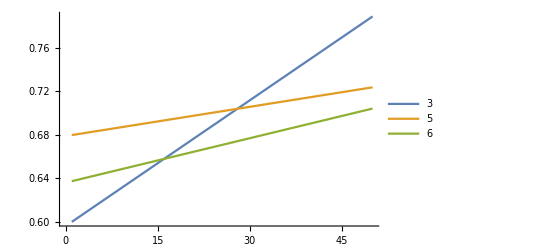

```mathematica
ListPlot[{Flatten[three],Flatten[five],Flatten[six]},Joined->True,PlotLegends->{"3","5","6","fivetwo","xfive","xsix"}]
```

```mathematica
pts=Graphics`Mesh`FindIntersections@Show[ListPlot[three,Joined->True],ListPlot[five,Joined->True],ListPlot[six,Joined->True]]
```

{{16.0189,0.657882},{27.9771,0.703909}}

```mathematica
xt=Table[{10*i,N[5/10+i/10,2]},{i,0,5}]
```

{{0,0.5},{10,0.6},{20,0.7},{30,0.8},{40,0.9},{50,1.}}

```mathematica
Show[ListPlot[{Flatten[three],Flatten[five],Flatten[six]},Joined->True,PlotLegends->Placed[LineLegend[{"3","5","6"},LegendFunction->"Frame",LegendLayout->"Row",LegendMarkerSize->35],{{0.43,1.05},{0.9,1.8}}],FrameTicksStyle->Directive[Bold,13], Frame->{{True,True},{True,True}},FrameLabel->{Style["1-"λ,Bold,15],Style["Success Probability",Bold,15]},Epilog->{Text[Style["(0.6602, 0.6579)",Bold,13],{22,0.645}],Text[Style["(0.7798, 0.7039)",Bold,13],{22,0.72}]} ],Graphics[{RGBColor[0,0.7,0],PointSize->0.025,Point[pts]}],ImageSize->Large]
```

-Graphics-